```mathematica
Лабораторная работа 7
```

```mathematica
Задание 1. Статистический анализ
```

```mathematica
text = "Charles - это веб-прокси (HTTP Proxy / HTTP Monitor), который работает на вашем собственном компьютере. Затем ваш веб-браузер (или любое другое интернет-приложение) настраивается для доступа к Интернету через Charles, после чего Charles может записывать и отображать для вас все отправляемые и получаемые данные. В веб- и интернет-разработке вы не можете видеть, что отправляется и принимается между вашим веб-браузером/клиентом и сервером. Без этой видимости трудно и требует много времени точно определить, где находится неисправность. Charles позволяет легко увидеть, что происходит, чтобы вы могли быстро диагностировать и устранять проблемы.";
```

```mathematica
charText = Characters[text] (*предварительная обработка текста, разбиваем на буквы*)
```

{C,h,a,r,l,e,s, ,-, ,э,т,о, ,в,е,б,-,п,р,о,к,с,и, ,(,H,T,T,P, ,P,r,o,x,y, ,/, ,H,T,T,P, ,M,o,n,i,t,o,r,),,, ,к,о,т,о,р,ы,й, ,р,а,б,о,т,а,е,т, ,н,а, ,в,а,ш,е,м, ,с,о,б,с,т,в,е,н,н,о,м, ,к,о,м,п,ь,ю,т,е,р,е,., ,З,а,т,е,м, ,в,а,ш, ,в,е,б,-,б,р,а,у,з,е,р, ,(,и,л,и, ,л,ю,б,о,е, ,д,р,у,г,о,е, ,и,н,т,е,р,н,е,т,-,п,р,и,л,о,ж,е,н,и,е,), ,н,а,с,т,р,а,и,в,а,е,т,с,я, ,д,л,я, ,д,о,с,т,у,п,а, ,к, ,И,н,т,е,р,н,е,т,у, ,ч,е,р,е,з, ,C,h,a,r,l,e,s,,, ,п,о,с,л,е, ,ч,е,г,о, ,C,h,a,r,l,e,s, ,м,о,ж,е,т, ,з,а,п,и,с,ы,в,а,т,ь, ,и, ,о,т,о,б,р,а,ж,а,т,ь, ,д,л,я, ,в,а,с, ,в,с,е, ,о,т,п,р,а,в,л,я,е,м,ы,е, ,и, ,п,о,л,у,ч,а,е,м,ы,е, ,д,а,н,н,ы,е,., ,В, ,в,е,б,-, ,и, ,и,н,т,е,р,н,е,т,-,р,а,з,р,а,б,о,т,к,е, ,в,ы, ,н,е, ,м,о,ж,е,т,е, ,в,и,д,е,т,ь,,, ,ч,т,о, ,о,т,п,р,а,в,л,я,е,т,с,я, ,и, ,п,р,и,н,и,м,а,е,т,с,я, ,м,е,ж,д,у, ,в,а,ш,и,м, ,в,е,б,-,б,р,а,у,з,е,р,о,м,/,к,л,и,е,н,т,о,м, ,и, ,с,е,р,в,е,р,о,м,., ,Б,е,з, ,э,т,о,й, ,в,и,д,и,м,о,с,т,и, ,т,р,у,д,н,о, ,и, ,т,р,е,б,у,е,т, ,м,н,о,г,о, ,в,р,е,м,е,н,и, ,т,о,ч,н,о, ,о,п,р,е,д,е,л,и,т,ь,,, ,г,д,е, ,н,а,х,о,д,и,т,с,я, ,н,е,и,с,п,р,а,в,н,о,с,т,ь,., ,C,h,a,r,l,e,s, ,п,о,з,в,о,л,я,е,т, ,л,е,г,к,о, ,у,в,и,д,е,т,ь,,, ,ч,т,о, ,п,р,о,и,с,х,о,д,и,т,,, ,ч,т,о,б,ы, ,в,ы, ,м,о,г,л,и, ,б,ы,с,т,р,о, ,д,и,а,г,н,о,с,т,и,р,о,в,а,т,ь, ,и, ,у,с,т,р,а,н,я,т,ь, ,п,р,о,б,л,е,м,ы,.}

```mathematica
unionText = Union[charText]
```

{(,),-,.,,,/, ,Б,В,З,И,а,б,в,г,д,е,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,х,ч,ш,ы,ь,э,ю,я,a,C,e,h,H,i,l,M,n,o,P,r,s,t,T,x,y}

```mathematica
replaceText = {"("->ls,")"->rs,"."->dot,","->c," "->s, "/"->sl,"-"->def};
```

```mathematica
newText = charText/.replaceText
```

{C,h,a,r,l,e,s,s,def,s,э,т,о,s,в,е,б,def,п,р,о,к,с,и,s,ls,H,T,T,P,s,P,r,o,x,y,s,sl,s,H,T,T,P,s,M,o,n,i,t,o,r,rs,c,s,к,о,т,о,р,ы,й,s,р,а,б,о,т,а,е,т,s,н,а,s,в,а,ш,е,м,s,с,о,б,с,т,в,е,н,н,о,м,s,к,о,м,п,ь,ю,т,е,р,е,dot,s,З,а,т,е,м,s,в,а,ш,s,в,е,б,def,б,р,а,у,з,е,р,s,ls,и,л,и,s,л,ю,б,о,е,s,д,р,у,г,о,е,s,и,н,т,е,р,н,е,т,def,п,р,и,л,о,ж,е,н,и,е,rs,s,н,а,с,т,р,а,и,в,а,е,т,с,я,s,д,л,я,s,д,о,с,т,у,п,а,s,к,s,И,н,т,е,р,н,е,т,у,s,ч,е,р,е,з,s,C,h,a,r,l,e,s,c,s,п,о,с,л,е,s,ч,е,г,о,s,C,h,a,r,l,e,s,s,м,о,ж,е,т,s,з,а,п,и,с,ы,в,а,т,ь,s,и,s,о,т,о,б,р,а,ж,а,т,ь,s,д,л,я,s,в,а,с,s,в,с,е,s,о,т,п,р,а,в,л,я,е,м,ы,е,s,и,s,п,о,л,у,ч,а,е,м,ы,е,s,д,а,н,н,ы,е,dot,s,В,s,в,е,б,def,s,и,s,и,н,т,е,р,н,е,т,def,р,а,з,р,а,б,о,т,к,е,s,в,ы,s,н,е,s,м,о,ж,е,т,е,s,в,и,д,е,т,ь,c,s,ч,т,о,s,о,т,п,р,а,в,л,я,е,т,с,я,s,и,s,п,р,и,н,и,м,а,е,т,с,я,s,м,е,ж,д,у,s,в,а,ш,и,м,s,в,е,б,def,б,р,а,у,з,е,р,о,м,sl,к,л,и,е,н,т,о,м,s,и,s,с,е,р,в,е,р,о,м,dot,s,Б,е,з,s,э,т,о,й,s,в,и,д,и,м,о,с,т,и,s,т,р,у,д,н,о,s,и,s,т,р,е,б,у,е,т,s,м,н,о,г,о,s,в,р,е,м,е,н,и,s,т,о,ч,н,о,s,о,п,р,е,д,е,л,и,т,ь,c,s,г,д,е,s,н,а,х,о,д,и,т,с,я,s,н,е,и,с,п,р,а,в,н,о,с,т,ь,dot,s,C,h,a,r,l,e,s,s,п,о,з,в,о,л,я,е,т,s,л,е,г,к,о,s,у,в,и,д,е,т,ь,c,s,ч,т,о,s,п,р,о,и,с,х,о,д,и,т,c,s,ч,т,о,б,ы,s,в,ы,s,м,о,г,л,и,s,б,ы,с,т,р,о,s,д,и,а,г,н,о,с,т,и,р,о,в,а,т,ь,s,и,s,у,с,т,р,а,н,я,т,ь,s,п,р,о,б,л,е,м,ы,dot}

```mathematica
Length[newText] (*количество всех символов в тексте*)
```

646

```mathematica
unionNewText = Union[newText] (*множество всех символов в тексте*)
```

{Б,В,З,И,а,б,в,г,д,е,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,х,ч,ш,ы,ь,э,ю,я,a,C,e,h,H,i,l,M,n,o,P,r,s,t,T,x,y,c,def,dot,ls,rs,s,sl}

```mathematica
Length[unionNewText]
```

56

```mathematica
defPos = Flatten[Position[newText, def] ](*места дефисов в данном тексте*)
```

{9,18,118,153,319,331,410}

```mathematica
spacePos = Flatten[Position[newText, s]]
(*s-пробелы*)
```

{8,10,14,25,31,37,39,44,54,62,71,74,80,92,104,110,114,126,131,137,144,165,179,183,191,193,203,209,218,224,229,237,243,254,256,267,271,275,279,292,294,305,313,315,320,322,342,345,348,355,363,367,380,382,394,400,406,429,431,441,445,450,460,467,469,477,483,491,497,509,513,523,538,546,556,562,571,575,587,593,596,602,609,625,627,637}

```mathematica
Length[spacePos]
```

86

```mathematica
unionDotC = Flatten[Union[Position[newText,dot], Position[newText,c]]]
(*dot - точки*)(*c - запятые*)
```

{53,103,217,312,362,440,508,537,570,586,646}

```mathematica
Position[newText,dot]
(*dot - точки*)
```

{{103},{312},{440},{537},{646}}

```mathematica
Position[newText, c]
(*c - запятые*)
```

{{53},{217},{362},{508},{570},{586}}

```mathematica
lengthSigns = Length[unionDotC] +Length[spacePos] +Length[defPos];
freqLetters = N[((Length[newText] - lengthSigns)/Length[newText])*100 ]
(*Вывод: частота букв в тексте~83.9*)
```

83.9009

```mathematica
freqSpaces = N[(Length[spacePos]/Length[newText])*100]
(*частота пробелов*)
```

13.3127

```mathematica
data=RandomInteger[{10,70},7](*7 случайных целых чисел от 10 до 70*)
```

{46,38,57,27,40,14,53}

```mathematica
N[Mean[data]](*находит среднее значение*)
```

39.2857

```mathematica
Max[data](*Находит максимальное значение*)
```

57

```mathematica
Задание 2. Метод Монте-Карло
```

```mathematica
pairs=RandomReal[{-1,1},{10000,2}];
pairs2=RandomReal[{-1,1},{10,2}]
```

{{-0.738623,-0.366051},{0.326841,0.959802},{0.792148,0.00932413},{-0.838463,-0.728956},{0.937796,-0.28174},{0.841722,-0.474946},{0.249497,-0.998249},{0.367586,0.474497},{-0.0124254,-0.872197},{-0.315295,0.346953}}

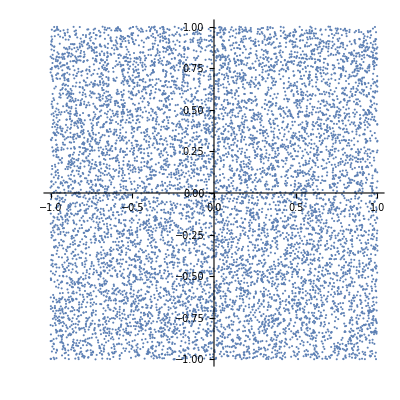

```mathematica
lp=ListPlot[pairs,AspectRatio->1]
```

```mathematica
(*Для приблизительного вычисленияπ,умножим площадь квадрата на процентное соотношение точек,попадающих в круг радиусом 1 с центром в начале координат.
Умножим площадь квадрата (в данном случае 4) на относительную массу точек,находящихся внутри круга:
*)
4*Count[Map[Norm,pairs],_?(#≤1&)]/10000.
```

3.1408

```mathematica
3. прогноз погоды
```

```mathematica
WeatherForecastData["Temperature",DateObject[Tomorrow, TimeObject[{15}]]]
```

(-8.4to-7.3) °C

```mathematica
WeatherForecastData[LinguisticAssistant,"MinTemperature"]["Values"]//Normal
(*["Values"]//Normal*)
```

{-11.1 °C,-7.6 °C,-9.2 °C,-9.4 °C,-5.3 °C,-5.5 °C,-1.5 °C,-0.7 °C}